```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\projects\bdnewsvis\bd_news_vis\prim_analysis

```mathematica
data=Import["OrganizedFile.csv"];
```

```mathematica
data[[2]]
```

{2011,10,12,1, Mushfiqur,PERSON}

```mathematica
people=Select[data,#[[6]]=="PERSON"&];
```

```mathematica
people[[100]]
```

{2011,10,12,93, Tota,PERSON}

```mathematica
Tally[people[[;;,5]]]
```

{{ Mushfiqur,141},{ Rahim,280},{ Khaleda,2026},{ Zia,2216},{ Doel,6},{ Hasina,4112},{ Shamim,165},{ Osman,150},27642,{ Iswarchandra,1},{ Vidyasagar,1},{ Nishi,1},{ Ittefaq,1},{ Paulinich,1},{ Padmo,1},{ Swarachitra,1},{ Chaskielberg,1}}
 |  |  |  |

```mathematica
tseries[topic_,type_]:=Module[
{topics,sel,tb},
topics=Select[data,#[[6]]==type&];
sel=Select[topics,StringTrim[#[[5]]]==topic&];
tb=Table[{sel[[i,1;;3]],sel[[i,4]]},{i,1,Length[sel]}];
Return[
Tally[tb[[;;,1]]]
]
]
```

```mathematica
ts=tseries["Shamim","PERSON"];
```

```mathematica
ts;
```

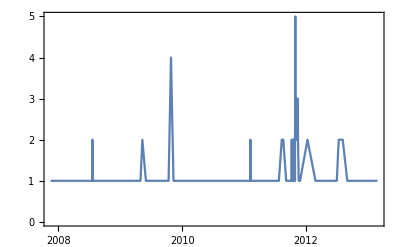

```mathematica
DateListPlot[ts,Joined->True,MaxPlotPoints->All,PlotRange->All]
```

```mathematica
Length[Abs[Fourier[Normalize[ts[[;;,2]]]]]]
```

1136

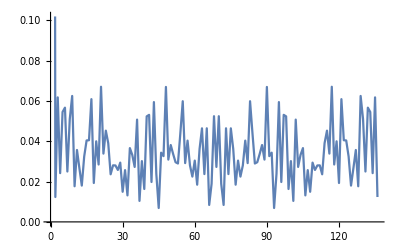

```mathematica
ListLinePlot[Abs[Fourier[Normalize[ts[[;;,2]]]]]]
```